```mathematica
(* These are VERY accurate Born-Oppeneimer energies from K. Pachucki, Phys Rev. A 82, 032509 (2010) *)
energies={{0.1,7.1272167311320000},{0.2,2.1978032952261800},{0.3,0.6192416597962260},{0.4,-0.1202303411788230},{0.5,-0.5266387587430010},{0.6,-0.7696354294859090},{0.7,-0.9220274615274640},{0.8,-1.0200566663605200},{0.9,-1.0836432399588300},{1,-1.1245397195468700},{1.1,-1.1500573677385700},{1.2,-1.1649352434403100},{1.25,-1.1694196273909000},{1.3,-1.1723471490380900},{1.32,-1.1731387363334800},{1.34,-1.1737348749583500},{1.36,-1.1741484985704200},{1.38,-1.1743916836322500},{1.39,-1.1744529172784600},{1.4,-1.1744757142204400},{1.41,-1.1744613708706800},{1.42,-1.1744111412392300},{1.44,-1.1742078365851000},{1.46,-1.1738750427492000},{1.48,-1.1734214182920800},{1.5,-1.1728550795785800},{1.55,-1.1709949198970200},{1.6,-1.1685833733714600},{1.7,-1.1624587268984600},{1.8,-1.1550687376116100},{1.9,-1.1468506970296900},{2,-1.1381329571326500},{2.1,-1.1291638361013200},{2.2,-1.1201321168492200},{2.3,-1.1111817652044400},{2.4,-1.1024226060113300},{2.5,-1.0939381299558800},{2.6,-1.0857912373961300},{2.7,-1.0780284841838300},{2.8,-1.0706832334814300},{2.9,-1.0637780088060200},{3,-1.0573262688726600},{3.1,-1.0513337722680200},{3.2,-1.0457996614324300},{3.3,-1.0407173653514000},{3.4,-1.0360753951907600},{3.5,-1.0318580848550900},{3.6,-1.0280463083797300},{3.7,-1.0246181884109600},{3.8,-1.0215497955336500},{3.9,-1.0188158276965000},{4,-1.0163902529506700},{4.2,-1.0123599596831700},{4.4,-1.0092565162615900},{4.6,-1.0068952238227400},{4.8,-1.0051160061003800},{5,-1.0037856585839700},{5.2,-1.0027968163112500},{5.4,-1.0020650572097100},{5.6,-1.0015252518866100},{5.8,-1.0011278808524200},{6,-1.0008357076551800},{6.5,-1.0004005485345400},{7,-1.0001979144800400},{7.5,-1.0001021061478100},{8,-1.0000556049730700},{8.5,-1.0000321718328300},{9,-1.0000197818324900},{9.5,-1.0000128568768300},{10,-1.0000087557460500},{10.5,-1.0000061899951100},{11,-1.0000045059894400},{11.5,-1.0000033561745800},{12,-1.0000025459695300},{13,-1.0000015292866700},{14,-1.0000009606807900},{15,-1.0000006254536300},{16,-1.0000004195863100},{17,-1.0000002888262400},{18,-1.0000002033405100},{19,-1.0000001460282400},{20,-1.0000001067401300}};

(* coeffs from table 5 of Ovsiannikov and Mitroy 2006 J. Phys. B: At. Mol. Opt. Phys. 39, 159-187 *)
(* Note that the accuracy of this asymptotic expansion, truncated at order r^30, 7*10^15 at r=20 a0 (a little worse that the ab initio), 10^-15 at r=21, 2*10^-16 at r=22 and 3*10^-17 at r= 23;   *)
cf={{6,6.499026705406},{8,1.243990835836*10^2},{10,3.285828414967*10^3},{11,-3.474898037882*10^3},{12,1.227276087007*10^5},{13,−3.269869240441*10^5},{14,6.361736045092*10^6},{15,-2.839558063300*10^7},{16,4.412051922739*10^8},{17,−2.739281653140*10^9},{18,3.935247733460*10^10},{19,−3.070824593893*10^11},{20,4.363762779418*10^12},{21,−4.036038399660*10^13},{22,5.860305164046*10^14},{23,−6.200210182655*10^15},{24,9.343361665*10^16},{25,−1.105388542*10^18},{26,1.741412160*10^19},{27,−2.268395655*10^20},{28,3.747400664*10^21},{29,−5.314885509*10^22},{30,9.215758*10^23}};
asymptoteLong=-1+Sum[(-cf[[i,2]])/r^cf[[i,1]],{i,1,23}];
energiesLong=Table[{r,asymptoteLong},{r,21,30,1}];
(* Super-short bond length extrapolation -- r < 0.1 a0 *)
asymptoteShort=1/r-2.903724377034119598+3.7917543333333334 r^2-6.9764351672132445 r^3;
(* Build approximant -- se my report for more info on this choice *)
rule={x_,y_}->{(x-1.5)/(x+1.5),y-1/x};
intR=Interpolation[Join[{{-1,-2.903724377034119598}},Sort[Join[energies,energiesLong]/.rule],{{1,-1}}],Method->"Spline",InterpolationOrder->9];
PECBO[r_]=intR[(r-1.5)/(r+1.5)]+1/r;
re=FindRoot[PECBO'[r]==0,{r,1.4}][[1,2]];
```

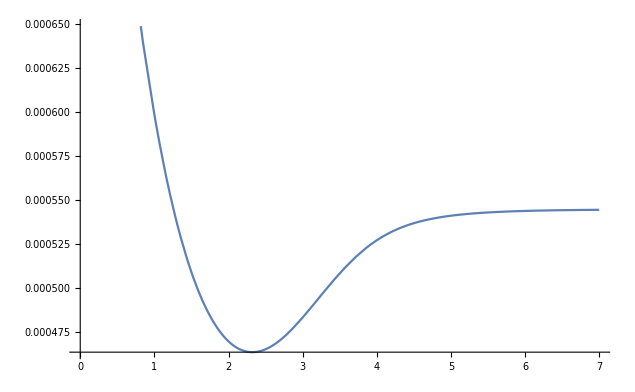

```mathematica
(* these are very accurate adiabatic PEC points from Pachucki and Komasa, J Chem Phys 141, 224103 (2014) *)
(* these are the mass-independent values, they should be divided by (2*μn) *)
mp=1836.15267377+0*0.00000017;
μ=(1/mp+1/mp)^-1;

dataadiabatic={{0,1.53139692606},{0.1,1.55095810021},{0.2,1.54810246202},{0.3,1.51061637414},{0.35,1.48343936864},{0.4,1.45300938055},{0.45,1.42067696707},{0.5,1.38746488006},{0.55,1.3541247326},{0.6,1.32119546419},{0.65,1.28905407678},{0.7,1.25795651479},{0.75,1.22806937296},{0.8,1.19949397118},{0.85,1.17228440512},{0.9,1.14646097538},{0.95,1.12202012713},{1.,1.09894177857},{1.05,1.07719470546},{1.1,1.05674048207},{1.15,1.0375363514},{1.2,1.01953730162},{1.25,1.00269755389},{1.3,0.986971613714},{1.32,0.980983093331},{1.34,0.975162863317},{1.36,0.969508181666},{1.38,0.964016351899},{1.39,0.961330676863},{1.4,0.95868472543},{1.4011,0.958396081986},{1.405,0.957376544913},{1.41,0.956078174316},{1.42,0.953510703442},{1.44,0.948491738318},{1.449,0.946283124517},{1.46,0.943625334674},{1.48,0.938909050051},{1.5,0.934340495289},{1.55,0.923550229153},{1.6,0.913633773608},{1.65,0.904558107268},{1.7,0.896292149182},{1.8,0.882074017855},{1.9,0.870764620658},{2.,0.862170945858},{2.1,0.856115986498},{2.2,0.852432649972},{2.30,0.850957550559},{2.35,0.850996542639},{2.4,0.851524934042},{2.5,0.853961054324},{2.6,0.858079416594},{2.7,0.863677387075},{2.8,0.870534706921},{2.9,0.878414396024},{3.,0.887066358688},{3.1,0.896233697879},{3.2,0.905661337333},{3.3,0.915106115057},{3.4,0.924347155575},{3.5,0.933195163296},{3.6,0.941499379332},{3.7,0.94915130999},{3.8,0.956084885196},{3.9,0.962273299755},{4.,0.967723281613},{4.2,0.976558381612},{4.4,0.983033195995},{4.6,0.987680270678},{4.8,0.990988213951},{5.,0.993346349776},{5.2,0.995040257943},{5.4,0.996269883897},{5.6,0.997172293732},{5.8,0.997841172093},{6.,0.99834112628},{6.5,0.999117827776},{7.,0.999511361323},{7.5,0.999716677766},{8.,0.999827480672},{8.5,0.999889772815},{9.,0.99992644},{9.5,0.99994906116},{10.,0.999963643443},{10.5,0.999973410827},{11.,0.99998016545},{11.5,0.999984959857},{12.,0.999988435895}};
asymptote[r_]=1-2μ (0.017699/r^6+0.144/r^8+2.28/r^10);
rule={x_,y_}->{(x-1.5)/(x+1.5),y};
data=Join[dataadiabatic,Table[{r,asymptote[r]},{r,12.5,30,0.5}]];
ff=Interpolation[data/.rule,Method->"Spline",InterpolationOrder->9];
adiabatic[r_]=1/(2μ)ff[(r-1.5)/(r+1.5)];
Plot[{ adiabatic[r]},{r,0,7},PlotRange->Automatic]
```

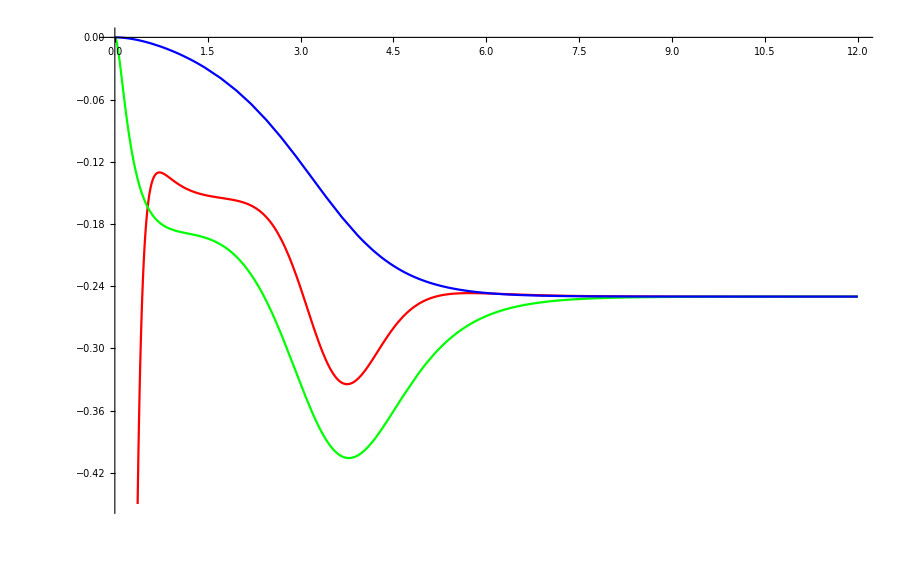

```mathematica
(* These are the non-adiabatic position dependent masses and potential from Pachucki, Komasa, J Chem Phys 143, 034111 (2015), from the supplementary material*)
dataWpar={{0.1000,-0.033969420054750},{0.2000,-0.081827908127400},{0.3000,-0.118544921458400},{0.3500,-0.132324146135900},{0.4000,-0.143550860197700},{0.4500,-0.152644223476300},{0.5000,-0.159983306625700},{0.5500,-0.165892752570600},{0.6000,-0.170643235933700},{0.6500,-0.174457465926500},{0.7000,-0.177517634204500},{0.7500,-0.179972596879300},{0.8000,-0.181944170898600},{0.8500,-0.183532407626000},{0.9000,-0.184819905446100},{0.9500,-0.185875292135200},{1.0000,-0.186756019267400},{1.0500,-0.187510599196000},{1.1000,-0.188180395821500},{1.1500,-0.188801060308500},{1.2000,-0.189403684859800},{1.2500,-0.190015732417800},{1.3000,-0.190661787719800},{1.3200,-0.190934794855000},{1.3400,-0.191218176015900},{1.3600,-0.191513233032600},{1.3800,-0.191821230822200},{1.3900,-0.191980468599900},{1.4000,-0.192143401019400},{1.4011,-0.192161555570500},{1.4050,-0.192226299442600},{1.4100,-0.192310177380200},{1.4200,-0.192480945301700},{1.4400,-0.192835038430500},{1.4490,-0.193000086786700},{1.4600,-0.193206831024800},{1.4800,-0.193597452085900},{1.5000,-0.194008011285500},{1.5500,-0.195128770059800},{1.6000,-0.196397607679000},{1.6500,-0.197830743360100},{1.7000,-0.199444038447100},{1.8000,-0.203273090060900},{1.9000,-0.208005827872200},{2.0000,-0.213757395328400},{2.1000,-0.220633272235300},{2.2000,-0.228722925172700},{2.3000,-0.238090852486400},{2.3500,-0.243264748727600},{2.4000,-0.248765250655000},{2.5000,-0.260724921435400},{2.6000,-0.273885587064000},{2.7000,-0.288087420667900},{2.8000,-0.303086197613600},{2.9000,-0.318550825638900},{3.0000,-0.334069873048400},{3.1000,-0.349168878428000},{3.2000,-0.363338633464300},{3.3000,-0.376072473922900},{3.4000,-0.386908365142200},{3.5000,-0.395469885554700},{3.6000,-0.401499715883200},{3.7000,-0.404880248246400},{3.8000,-0.405638269031000},{3.9000,-0.403933710479700},{4.0000,-0.400035348524600},{4.2000,-0.387078779702700},{4.4000,-0.369830983118500},{4.6000,-0.351109271785800},{4.8000,-0.332980176922700},{5.0000,-0.316668034964400},{5.2000,-0.302707771994100},{5.4000,-0.291172137361200},{5.6000,-0.281874429505100},{5.8000,-0.274512838369400},{6.0000,-0.268758564651900},{6.5000,-0.259475449442000},{7.0000,-0.254733387628700},{7.5000,-0.252355354345800},{8.0000,-0.251174105362600},{8.5000,-0.250589762059600},{9.0000,-0.250300563926100},{9.5000,-0.250156641200500},{10.0000,-0.250084179264200},{10.5000,-0.250047005044400},{11.0000,-0.250027420036500},{11.5000,-0.250016742992800},{12.0000,-0.250010683362900}};
dataWperp={{0.1000,-0.000209775882038},{0.2000,-0.000808434386423},{0.3000,-0.001740301664823},{0.3500,-0.002315592728917},{0.4000,-0.002957170259736},{0.4500,-0.003661113149213},{0.5000,-0.004424234582093},{0.5500,-0.005243988609890},{0.6000,-0.006118382535950},{0.6500,-0.007045899300115},{0.7000,-0.008025430785265},{0.7500,-0.009056221458142},{0.8000,-0.010137821117209},{0.8500,-0.011270045516342},{0.9000,-0.012452943484968},{0.9500,-0.013686769461005},{1.0000,-0.014971960418267},{1.0500,-0.016309116349692},{1.1000,-0.017698983588253},{1.1500,-0.019142440363334},{1.2000,-0.020640484079215},{1.2500,-0.022194219878194},{1.3000,-0.023804850108548},{1.3200,-0.024465318801101},{1.3400,-0.025135182207369},{1.3600,-0.025814528352795},{1.3800,-0.026503447051262},{1.3900,-0.026851524639268},{1.4000,-0.027202029805514},{1.4011,-0.027240734078299},{1.4050,-0.027378196378436},{1.4100,-0.027554974235199},{1.4200,-0.027910369706395},{1.4400,-0.028628561330527},{1.4490,-0.028954987205007},{1.4600,-0.029356700636046},{1.4800,-0.030094884856063},{1.5000,-0.030843212389470},{1.5500,-0.032759063155469},{1.6000,-0.034740510898124},{1.6500,-0.036789157304213},{1.7000,-0.038906615578517},{1.8000,-0.043354390827350},{1.9000,-0.048096391512233},{2.0000,-0.053144277834276},{2.1000,-0.058508112778829},{2.2000,-0.064195533807134},{2.3000,-0.070210801844895},{2.3500,-0.073341528771299},{2.4000,-0.076553746624409},{2.5000,-0.083218648232807},{2.6000,-0.090193119473731},{2.7000,-0.097457080038176},{2.8000,-0.104981937379577},{2.9000,-0.112730104766772},{3.0000,-0.120654987456741},{3.1000,-0.128701547098521},{3.2000,-0.136807508995314},{3.3000,-0.144905208488064},{3.4000,-0.152923989804857},{3.5000,-0.160792987614338},{3.6000,-0.168444055727695},{3.7000,-0.175814574738949},{3.8000,-0.182849879951811},{3.9000,-0.189505101755674},{4.0000,-0.195746291726297},{4.2000,-0.206906970112877},{4.4000,-0.216276864417789},{4.6000,-0.223939972007415},{4.8000,-0.230071222612934},{5.0000,-0.234889541186647},{5.2000,-0.238621712111829},{5.4000,-0.241479435731032},{5.6000,-0.243647670979827},{5.8000,-0.245280885670142},{6.0000,-0.246504028951299},{6.5000,-0.248362744597865},{7.0000,-0.249238312074045},{7.5000,-0.249645853434350},{8.0000,-0.249834403368399},{8.5000,-0.249921551116579},{9.0000,-0.249962009969813},{9.5000,-0.249980999639428},{10.0000,-0.249990082448114},{10.5000,-0.249994551021725},{11.0000,-0.249996834760312},{11.5000,-0.249998057813077},{12.0000,-0.249998747997916}};
datau={{0.1000,-8.405274888404050},{0.2000,-4.736193666532090},{0.3000,-2.955291539154040},{0.3500,-2.409641480204120},{0.4000,-2.000079514971490},{0.4500,-1.686397334830480},{0.5000,-1.441748653045050},{0.5500,-1.247809174871240},{0.6000,-1.091808044132700},{0.6500,-0.964670119653545},{0.7000,-0.859829360322755},{0.7500,-0.772455547286699},{0.8000,-0.698940607999289},{0.8500,-0.636551138533214},{0.9000,-0.583189304835060},{0.9500,-0.537225667537959},{1.0000,-0.497380534440205},{1.0500,-0.462638569827439},{1.1000,-0.432186531799611},{1.1500,-0.405367316543871},{1.2000,-0.381645649718142},{1.2500,-0.360582198191628},{1.3000,-0.341813839082456},{1.3200,-0.334879688327272},{1.3400,-0.328246876502112},{1.3600,-0.321899561861591},{1.3800,-0.315822962853308},{1.3900,-0.312881831825362},{1.4000,-0.310003275257412},{1.4011,-0.309690385635525},{1.4050,-0.308586964967272},{1.4100,-0.307185707957498},{1.4200,-0.304427596759482},{1.4400,-0.299083858208534},{1.4490,-0.296751809125094},{1.4600,-0.293960760896536},{1.4800,-0.289047719262110},{1.5000,-0.284334808497586},{1.5500,-0.273368383868793},{1.6000,-0.263465381871391},{1.6500,-0.254513667795184},{1.7000,-0.246416700824054},{1.8000,-0.232464460809153},{1.9000,-0.221064876670104},{2.0000,-0.211804813656352},{2.1000,-0.204367240886630},{2.2000,-0.198506903752758},{2.3000,-0.194033023529507},{2.3500,-0.192268175375871},{2.4000,-0.190796996508428},{2.5000,-0.188683749584401},{2.6000,-0.187605750374676},{2.7000,-0.187498744971259},{2.8000,-0.188318182437592},{2.9000,-0.190035106547354},{3.0000,-0.192630244501491},{3.1000,-0.196085327262642},{3.2000,-0.200371497710215},{3.3000,-0.205435951587047},{3.4000,-0.211189354373445},{3.5000,-0.217497478138625},{3.6000,-0.224180312770676},{3.7000,-0.231020406871557},{3.8000,-0.237779769921706},{3.9000,-0.244222206182760},{4.0000,-0.250136420858273},{4.2000,-0.259767319067850},{4.4000,-0.266019253963360},{4.6000,-0.269076292224461},{4.8000,-0.269639888813368},{5.0000,-0.268557771234611},{5.2000,-0.266576319138405},{5.4000,-0.264242104262764},{5.6000,-0.261902507578336},{5.8000,-0.259748966552259},{6.0000,-0.257867067603866},{6.5000,-0.254407659662740},{7.0000,-0.252380720898214},{7.5000,-0.251262771182314},{8.0000,-0.250665704422668},{8.5000,-0.250352415386625},{9.0000,-0.250189322846123},{9.5000,-0.250104357518060},{10.0000,-0.250059659643219},{10.5000,-0.250035679911990},{11.0000,-0.250022425872451},{11.5000,-0.250014808145106},{12.0000,-0.250010225529884}};
datav={{0.1000,0.529838533353434},{0.2000,0.613999178526620},{0.3000,0.579558287342369},{0.3500,0.550470562534196},{0.4000,0.519763556811376},{0.4500,0.489430590944021},{0.5000,0.460456969986223},{0.5500,0.433280436133537},{0.6000,0.408042995815502},{0.6500,0.384730084085033},{0.7000,0.363247957563274},{0.7500,0.343466750699476},{0.8000,0.325244229931121},{0.8500,0.308438610822335},{0.9000,0.292915156216633},{0.9500,0.278549246519517},{1.0000,0.265227470284356},{1.0500,0.252847630353291},{1.1000,0.241318183659365},{1.1500,0.230557413045548},{1.2000,0.220492500620738},{1.2500,0.211058596394498},{1.3000,0.202197931420381},{1.3200,0.198802441899068},{1.3400,0.195487327964307},{1.3600,0.192249683699061},{1.3800,0.189086730394735},{1.3900,0.187532427697454},{1.4000,0.185995810103974},{1.4011,0.185827848279521},{1.4050,0.185234034708437},{1.4100,0.184476563229446},{1.4200,0.182974379482063},{1.4400,0.180020003905620},{1.4490,0.178711786761182},{1.4600,0.177130351857642},{1.4800,0.174303189562986},{1.5000,0.171536375866362},{1.5500,0.164870094357474},{1.6000,0.158538480050023},{1.6500,0.152514454459435},{1.7000,0.146773383046010},{1.8000,0.136051735208410},{1.9000,0.126212882726271},{2.0000,0.117115820865779},{2.1000,0.108631345522331},{2.2000,0.100635211851125},{2.3000,0.093002396381676},{2.3500,0.089281868136900},{2.4000,0.085602868661080},{2.5000,0.078299575830426},{2.6000,0.070949555358977},{2.7000,0.063409104248491},{2.8000,0.055543615182755},{2.9000,0.047241941836986},{3.0000,0.038433988811409},{3.1000,0.029108838127431},{3.2000,0.019329540209152},{3.3000,0.009240257698453},{3.4000,-0.000937784207894},{3.5000,-0.010923012204823},{3.6000,-0.020401400796508},{3.7000,-0.029061131968015},{3.8000,-0.036627715465475},{3.9000,-0.042893122538549},{4.0000,-0.047734111069380},{4.2000,-0.053094507865897},{4.4000,-0.053351141838088},{4.6000,-0.049903056420202},{4.8000,-0.044299463710904},{5.0000,-0.037835071351658},{5.2000,-0.031402117664721},{5.4000,-0.025515133760633},{5.6000,-0.020406883411158},{5.8000,-0.016130069993160},{6.0000,-0.012637379016503},{6.5000,-0.006691777406608},{7.0000,-0.003468790779029},{7.5000,-0.001781605382649},{8.0000,-0.000914554776534},{8.5000,-0.000473057497065},{9.0000,-0.000248736319129},{9.5000,-0.000134216879417},{10.0000,-0.000075020433020},{10.5000,-0.000043770346421},{11.0000,-0.000026771122321},{11.5000,-0.000017165261511},{12.0000,-0.000011494713299}};
dataδv={{0.1000,-1.490159828569000},{0.2000,-0.894837690577000},{0.3000,-0.563997834359800},{0.3500,-0.454103628668500},{0.4000,-0.368374198220800},{0.4500,-0.300703366882700},{0.5000,-0.246719330251700},{0.5500,-0.203242874155800},{0.6000,-0.167928508501200},{0.6500,-0.139022681149700},{0.7000,-0.115198210381300},{0.7500,-0.095439163929720},{0.8000,-0.078959661875150},{0.8500,-0.065145836111260},{0.9000,-0.053513821320460},{0.9500,-0.043678992543590},{1.0000,-0.035333191230580},{1.0500,-0.028227692109900},{1.1000,-0.022160341091150},{1.1500,-0.016965755087410},{1.2000,-0.012507791529830},{1.2500,-0.008673715841866},{1.3000,-0.005369650254204},{1.3200,-0.004178376123053},{1.3400,-0.003054749730746},{1.3600,-0.001994623698077},{1.3800,-0.000994120636537},{1.3900,-0.000515084803641},{1.4000,-0.000049612742340},{1.4011,0.000000779174157},{1.4050,0.000178167883213},{1.4100,0.000402713088950},{1.4200,0.000842296880443},{1.4400,0.001684791328015},{1.4490,0.002048594325440},{1.4600,0.002480855580210},{1.4800,0.003233290888253},{1.5000,0.003944727983279},{1.5500,0.005559818512695},{1.6000,0.006968528938599},{1.6500,0.008200835389009},{1.7000,0.009282652378133},{1.8000,0.011081824616420},{1.9000,0.012513287617980},{2.0000,0.013689163071000},{2.1000,0.014694539425560},{2.2000,0.015592583818690},{2.3000,0.016427577137150},{2.3500,0.016830527098950},{2.4000,0.017226560520360},{2.5000,0.018000195464610},{2.6000,0.018743423204470},{2.7000,0.019436509222320},{2.8000,0.020047018720220},{2.9000,0.020533133961770},{3.0000,0.020848459293090},{3.1000,0.020948072647430},{3.2000,0.020795143786640},{3.3000,0.020367078066080},{3.4000,0.019660008843720},{3.5000,0.018690654451290},{3.6000,0.017495069264960},{3.7000,0.016124513586530},{3.8000,0.014639318347680},{3.9000,0.013102012671400},{4.0000,0.011571004766210},{4.2000,0.008714199854117},{4.4000,0.006321608755328},{4.6000,0.004467861486532},{4.8000,0.003108514649072},{5.0000,0.002147349215773},{5.2000,0.001482256613720},{5.4000,0.001026785171938},{5.6000,0.000715599301491},{5.8000,0.000502366308110},{6.0000,0.000355367879635},{6.5000,0.000154391109855},{7.0000,0.000069872505897},{7.5000,0.000032865423235},{8.0000,0.000016117053762},{8.5000,0.000008294895697},{9.0000,0.000004510544399},{9.5000,0.000002600750189},{10.0000,0.000001588027833},{10.5000,0.000001020975607},{11.0000,0.000000685521551},{11.5000,0.000000476667186},{12.0000,0.000000340744742}};
(* for now perform a very simple extrapolation for r > 12; I did fits between 11 and 12 a0 (steps of 0.1), trying the form a+b/r^n and choosing the n which leads to the smallest a (I subtracted the asymtote, -0.25) *)
(* A slightly more complicated form was chosen for v, as we need its derivative and there is some sensitivity to extrapolation *)

Wpar=Interpolation[Join[{{0,0}},dataWpar,Table[{r,-0.25-(7.809753418076427*^6)/r^11},{r,12.5,30,0.5}]],Method->"Spline",InterpolationOrder->9];
Wperp=Interpolation[Join[{{0,0}},dataWperp,Table[{r,-0.25+904461.914086058/r^11},{r,12.5,30,0.5}]],Method->"Spline",InterpolationOrder->9];
u=Interpolation[Join[datau,Table[{r,-0.25-52424.5550248338/r^9},{r,12.5,30,0.5}]],Method->"Spline",InterpolationOrder->9];
v=Interpolation[Join[datav,Table[{r,-(3.1205152736332115*^24)/r^29-58485.567542946235/r^9},{r,12.5,30,0.5}]],Method->"Spline",InterpolationOrder->9];
δv=Interpolation[Join[dataδv,Table[{r,146.24462775235594/r^8},{r,12.5,30,0.5}]],Method->"Spline",InterpolationOrder->9];
nonadiabatic[r_]=u[r]+2/r(v[r]+δv[r])+v'[r]+δv'[r];
Plot[{nonadiabatic[r],Wpar[r],Wperp[r]},{r,0,12},PlotRange->{-0.45,0.},PlotStyle->{Red,Green,Blue}]
```

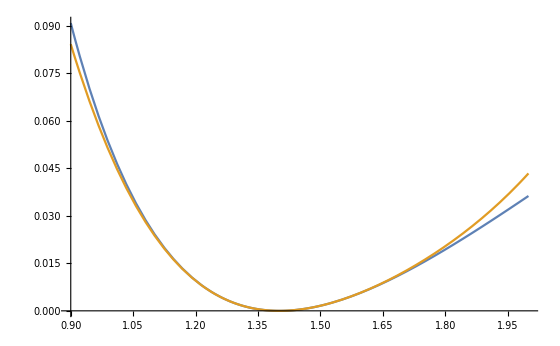

```mathematica
(* For future cross-tests with DUO, I do simple fits of the curves to simple forms *)
exact[r_]=(PECBO[r]-PECBO[re])+(adiabatic[r]-adiabatic[re])+nonadiabatic[r]/μ^2;
Plot[{exact[r],0.1848565(r-1.40147)^2-0.211461 (r-1.40147)^3+0.175647(r-1.40147)^4},{r,0.9,2.0}]
```

```mathematica
(* Here we include the non-adiabatic corrections in the Hamiltonian *)
Jrot=0;
(* These are, for J=0, 1, ... 31, the maximum nu in the linelist by Pachucki2009 *)
numax={14,14,14,14,13,13,13,13,12,12,12,11,11,10,10,9,9,8,8,7,7,6,6,5,4,4,3,2,2,1,1,0};
alleigv={};
Clear[Jrot];

Do[
V[r_]=(PECBO[r]-PECBO[re])+0(adiabatic[r]-adiabatic[re])+(Jrot(Jrot+1))/r^2(1/(2μ)+0 Wperp[r]/μ^2)+0 nonadiabatic[r]/μ^2+0 Wpar'[r]/(r μ^2);
Neigenvalues = 15;
Neigenvalues = numax[[Jrot+1]]+1;
xmin=0.4;xmax=18;
Npoints=200;
ℏ=1;
Neigenvalues=Min[Neigenvalues,Npoints];
Δx=(xmax-xmin)/(Npoints-1);
xs=Table[xmin+ i Δx,{i,0,Npoints-1}];

H=ℏ^2/(2μ Δx^2)Table[If[i==j,π^2/3 ,(2(-1)^(i-j))/(i-j)^2],{i,0,Npoints-1},{j,0,Npoints-1}];
W=1/Δx^2 Table[If[i==j,π^2/3 Wpar[ xs[[i+1]] ]/μ^2 ,(2(-1)^(i-j))/(i-j)^2 Wpar[ xs[[i+1]] ]/μ^2],{i,0,Npoints-1},{j,0,Npoints-1}];
X=1/Δx Table[If[i==j,0 ,-(-1)^(i-j)/(i-j)Wpar'[ xs[[i+1]] ]/μ^2],{i,0,Npoints-1},{j,0,Npoints-1}];
 H=H+0W+X; 
Do[H[[i+1,i+1]]=H[[i+1,i+1]]+V[ xs[[i+1]] ],{i,0,Npoints-1}]
eigv=Take[Sort[Eigenvalues[N[H]]],Neigenvalues];
alleigv=Join[alleigv,Table[{k-1,Jrot,(eigv[[k]])*219474.6313705},{k,1,Neigenvalues}]]
,{Jrot,0,1}]
```